```mathematica
dir=NotebookDirectory[];
SetDirectory@dir;
```

```mathematica
NotebookEvaluate[dir<>"../../../Tools/Mathematica/triangulation.nb"]
NotebookEvaluate[dir<>"../../../Tools/Mathematica/FEinterpolants.nb"]
```

## Mesh

```mathematica
𝒯=import@"mesh.ntr";
```

```mathematica
highlight[𝒯,{"trianglesNumn"},0]
```

## Interpolant

```mathematica
FE=ΔP2L;
```

```mathematica
ξ=Import["x.dat"][[1]];
```

```mathematica
ξInterpolant=interpolantOfξ[ξ,FE,𝒯];
```

### Plot

```mathematica
Plot3D[{ξInterpolant[x,y],u[x,y]},{x,y}∈Ω,Mesh->None,PlotRange->All]
```

```mathematica
DensityPlot[ξInterpolant[x,y],{x,y}∈Ω,ColorFunction->"TemperatureMap",PlotLegends->Automatic]
```

### L_2-Norm of Error

```mathematica
Pξ=𝒫[ξ,FE,𝒯];
```

```mathematica
densityPlot𝒫ξ[Pξ,𝒯,{-1,1},"TemperatureMap"]
```

```mathematica
Legended[DensityPlot[u[x,y],{x,y}∈Ω,ColorFunction->ColorData@{"TemperatureMap",{-1,1}}],BarLegend[{"TemperatureMap",{-1,1}}]]
```

```mathematica
Export["divgrad_u.png",Show[%307,ImageSize->300]]
```

divgrad_u.png

```mathematica
plot𝒫ξ[Pξ,𝒯]
```

```mathematica
Export["divgrad_l2_u.pdf",Show[%289,ImageSize->200]]
```

```mathematica
computeErrorNorm[u,Pξ,𝒯]
```

```mathematica
L1error={0.07115895042980311,0.02076859919507121,0.0055510662081776655,0.001418765194069177};
L2error={0.008191574895779891,0.001080062154608124,0.00013757872528474984,0.00001737188788759654};
CR1Error={0.05642615376501218,0.01540438811103093,0.0039482713099178324,0.0009942314556222313};
```

```mathematica
ScientificForm[#,3]&/@CR1Error
```

{5.64×10^-2,1.54×10^-2,3.95×10^-3,9.94×10^-4}

```mathematica
Table[ScientificForm[#[[i-1]]/#[[i]],3],{i,2,Length@#}]&@CR1Error
```

{3.66,3.9,3.97}

## Smoothing Properties

```mathematica
smoothers={
"relaxed Jacobi"->Import["residuals history/relaxed Jacobi.dat"],
"forward SOR"->Import["residuals history/forward SOR.dat"],
"backward SOR"->Import["residuals history/backward SOR.dat"],
"SSOR"->Import["residuals history/SSOR.dat"]
};
```

```mathematica
residulsNorms=Map[Norm,Last/@smoothers,{2}];
```

### Residuals’ Norms

```mathematica
plotOnly={1,2,3,4};
start=1;
showN=50;
```

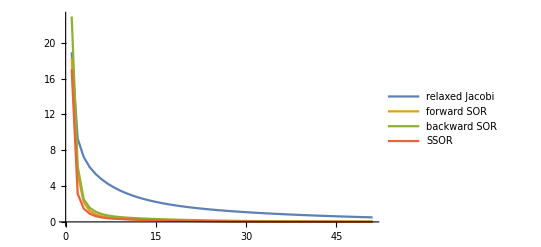

```mathematica
iters={start,Min[Length@First@residulsNorms,start+showN]};
ListLinePlot[Take[#,iters]&/@ residulsNorms[[plotOnly]],PlotLegends->Table[smoothers[[i,1]],{i,Length@smoothers}][[plotOnly]],PlotRange->All]
```

### Residuals’ Smoothing

```mathematica
solverNo=4;
```

```mathematica
f=interpolantOfξ[#,FE,𝒯]&/@smoothers[[solverNo,2]];
```

```mathematica
Manipulate[Plot3D[f[[i]][x,y],{x,y}∈Ω,PlotLabel->residulsNorms[[solverNo,i]],Mesh->None,ColorFunction->"TemperatureMap",PlotRange->{-1,1}],{i,1,Length@residulsNorms[[solverNo]],1}]
```

## Multigrid

```mathematica
ℓ=2;(* numb of mesh levels *)
```

### System Matrices

```mathematica
A=Table[Import["mg/A"<>ToString[i-1]<>".rsa"],{i,ℓ+1}];
```

```mathematica
MatrixPlot[#,MaxPlotPoints->Infinity]&/@A[[;;3]]
```

### Meshes

```mathematica
mesh=Table[import["mg/mesh"<>ToString[i-1]<>".ntr"],{i,ℓ+1}];
```

```mathematica
highlight[#,{"nodesNumn"},0]&/@mesh[[;;3]]
```

### Prolongation Matrices

```mathematica
prolongation=Table[Import["mg/P"<>ToString[i-1]<>".rra"],{i,ℓ}];
```

```mathematica
MatrixPlot[Transpose@#,MaxPlotPoints->Infinity]&/@prolongation[[;;2]]
```

### Prolongated Correction

```mathematica
correction=Import["mg/correction.dat"];
```

```mathematica
e1=𝒫[correction[[1]],FE,mesh[[1]]];
e2=𝒫[correction[[2]],FE,mesh[[2]]];
```

```mathematica
pe1=plot𝒫ξ[e1,mesh[[1]],{Red,Opacity@.7}]
```

-Graphics3D-

```mathematica
pe2=plot𝒫ξ[e2,mesh[[2]],{Green,Opacity@.7}]
```

-Graphics3D-

```mathematica
Show[pe1,pe2]
```

-Graphics3D-

### Resctricted Residual

```mathematica
residual=Import["mg/residual.dat"];
```

```mathematica
r2=𝒫[residual[[1]],FE,mesh[[2]]];
r1=𝒫[residual[[2]],FE,mesh[[1]]];
```

```mathematica
pr2=plot𝒫ξ[r2,mesh[[2]],{Red,Opacity@.7}]
```

-Graphics3D-

```mathematica
pr1=plot𝒫ξ[r1,mesh[[1]],{Green,Opacity@.7}]
```

-Graphics3D-

```mathematica
Show[pr2,pr1]
```

-Graphics3D-

```mathematica
Norm[.25*prolongation[[2]].residual[[1]]-residual[[2]]]
```

1.31683

## V-Cycle Log

```mathematica
vcycle=Import["mg/vcycle.dat"][[;;4]];
```

```mathematica
{min,max}={-1,1}(*{Min@Flatten@vcycle,Max@Flatten@vcycle};*)
```

{-1,1}

```mathematica
interpolants=𝒫[#,FE,𝒯]&/@vcycle;
```

```mathematica
plots=densityPlot𝒫ξ[#,𝒯,{min,max},"TemperatureMap"]&/@interpolants;
```

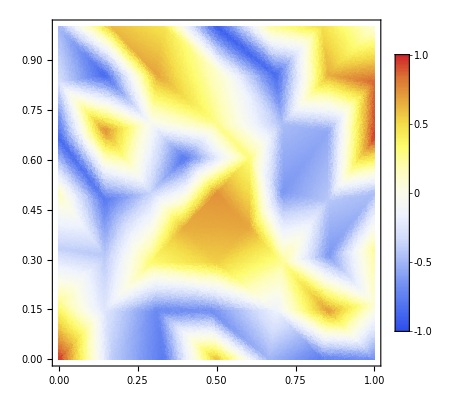
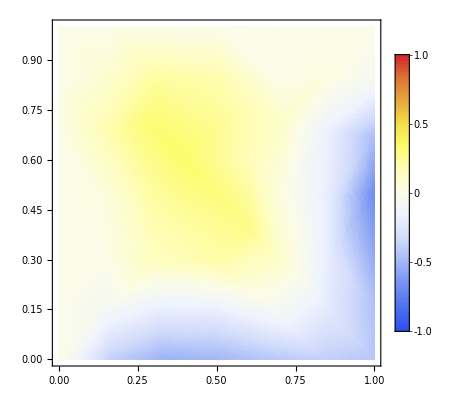
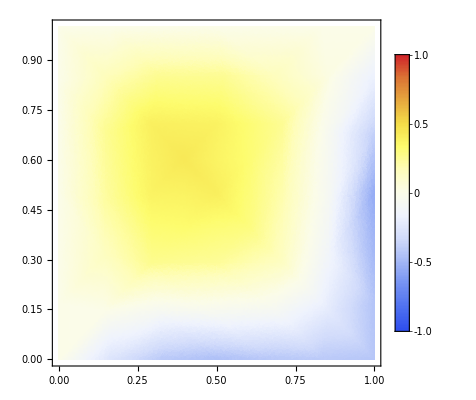
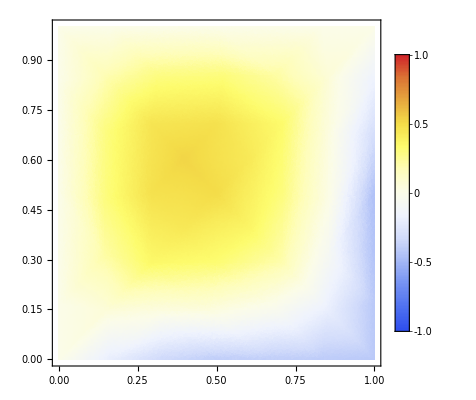

```mathematica
plots
```

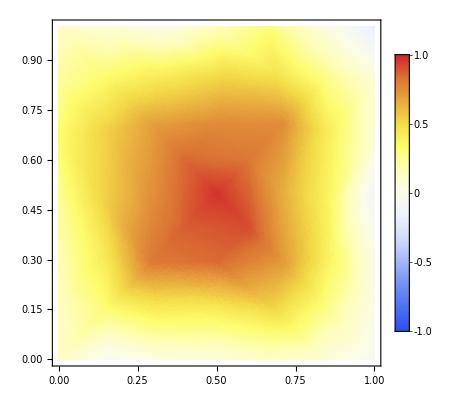
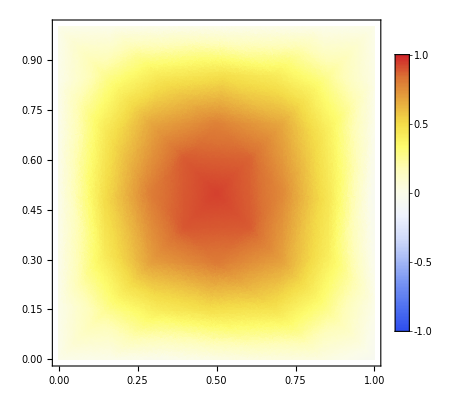
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plots
```

```mathematica
BarLegend[{"TemperatureMap",{-1,1}},LegendLayout->"Row"]
```

```mathematica
Show[%108,ImageSize->100]
```

Show::gtype: BarLegend is not a type of graphics.

Show[,ImageSize→100]

```mathematica
Export["shuffled guesses/x_0.dat",RandomVariate[UniformDistribution[{-1,1}],53]]
```

shuffled guesses/x_0.dat